## Definiciones

```mathematica
(* Función no recursiva para el tríángulo de Pascal para la DTQW con canal completamente dephasing *)
ClearAll[PositionDistributionDTQWwCompletelyDephasing]

PositionDistributionDTQWwCompletelyDephasing[t_,a_,b_]:=Module[{p},
p={Abs[a-b]^2/2,Abs[a+b]^2/2};(* probabilidades al tiempo t=1 *)
Do[p=Join[{p[[1]]},Table[Total[p[[i;;i+1]]],{i,j}],{p[[-1]]}]/2,{j,t-1}];(* probabilidades al tiempo t *)
Chop@Riffle[p,0](* meter ceros entre cada probabilidad *)
]
```

```mathematica
(* (en desuso porque es ineficiente para t>20) Función recursiva que implementa el triángulo de Pascal para la DTQW con completamente dephasing (i.e. p=0.5) *)
PositionDistributionDTQWwCompletelyDephasingDeprecated[0,0,a_,b_]:=1;PositionDistributionDTQWwCompletelyDephasingDeprecated[1,1,a_,b_]:=Abs[a+b]^2/2;PositionDistributionDTQWwCompletelyDephasingDeprecated[-1,1,a_,b_]:=Abs[a-b]^2/2;
PositionDistributionDTQWwCompletelyDephasingDeprecated[x_,t_,a_,b_]:=
Which[
EvenQ[x]==OddQ[t]||Abs[x]>t,0,
x==t,PositionDistributionDTQWwCompletelyDephasingDeprecated[x-1,t-1,a,b]/2,
-x==t,PositionDistributionDTQWwCompletelyDephasingDeprecated[x+1,t-1,a,b]/2,
Abs[x]!=t,(PositionDistributionDTQWwCompletelyDephasingDeprecated[x-1,t-1,a,b]+PositionDistributionDTQWwCompletelyDephasingDeprecated[x+1,t-1,a,b])/2
]
```

```mathematica
PascalRow[t_Integer]:=Riffle[Binomial[t,#]/(2^t)&@Range[0,t],0]
```

## Cálculos

```mathematica
(* Comparar triángulos de Pascal de la RW y de la DTQW con completamente dephasing *)

{xMin,xMax,tMin,tMax}={-5,5,0,5};

{a,b}={1/√2.,1/√2.};

{TableForm[N@Table[PositionDistributionDTQWwCompletelyDephasingDeprecated[#,t,a,b]&/@Range[xMin,xMax],{t,tMin,tMax}],TableHeadings->Map[ToString,{Range[tMin,tMax],Range[xMin,xMax]},{2}]],
TableForm[N@Table[Join[#,PascalRow[t],#]&[ConstantArray[0,tMax-t]],{t,tMin,tMax}],TableHeadings->Map[ToString,{Range[tMin,tMax],Range[xMin,xMax]},{2}]]}
```

{ | -5 | -4 | -3 | -2 | -1 | 0 | 1 | 2 | 3 | 4 | 5
0 | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
1 | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
2 | 0. | 0. | 0. | 0. | 0. | 0.5 | 0. | 0.5 | 0. | 0. | 0.
3 | 0. | 0. | 0. | 0. | 0.25 | 0. | 0.5 | 0. | 0.25 | 0. | 0.
4 | 0. | 0. | 0. | 0.125 | 0. | 0.375 | 0. | 0.375 | 0. | 0.125 | 0.
5 | 0. | 0. | 0.0625 | 0. | 0.25 | 0. | 0.375 | 0. | 0.25 | 0. | 0.0625, | -5 | -4 | -3 | -2 | -1 | 0 | 1 | 2 | 3 | 4 | 5
0 | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
1 | 0. | 0. | 0. | 0. | 0.5 | 0. | 0.5 | 0. | 0. | 0. | 0.
2 | 0. | 0. | 0. | 0.25 | 0. | 0.5 | 0. | 0.25 | 0. | 0. | 0.
3 | 0. | 0. | 0.125 | 0. | 0.375 | 0. | 0.375 | 0. | 0.125 | 0. | 0.
4 | 0. | 0.0625 | 0. | 0.25 | 0. | 0.375 | 0. | 0.25 | 0. | 0.0625 | 0.
5 | 0.03125 | 0. | 0.15625 | 0. | 0.3125 | 0. | 0.3125 | 0. | 0.15625 | 0. | 0.03125}

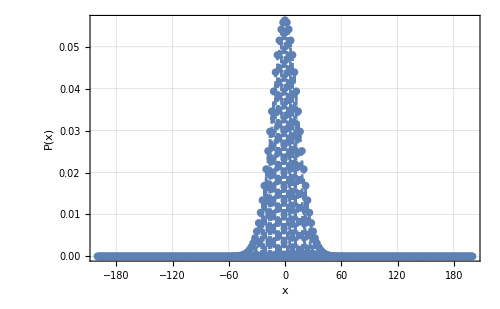

```mathematica
(* Graficar distribución de probabilidad de la DTQW con canal completamente dephasing *)

t=200;
{a,b}={1.,0.}(* Subscript[Subscript[ψ, 0], moneda] = a0+b1 *);

{xMin,xMax}={-t,t}(* límites en x para gráfica *);

ListPlot[Transpose[{Range[-t,t],PositionDistributionDTQWwCompletelyDephasing[t,a,b]}],
PlotRange->{{xMin,xMax},All},
Joined->True,PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,8},
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[x]],TraditionalForm[P[x]]},
FrameStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
GridLines->Automatic,GridLinesStyle->Directive[LightGray, Dashed],
ImageSize->500
]
```